## I . Introduction

```mathematica
(*Import["https://raw.githubusercontent.com/satfra/FunKit/main/FunKitInstaller.m"]*)
```

```mathematica
Get["FunKit`"]
```

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.2.0
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].


-Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
FSetGlobalSetup[<|"FieldSpace"-><|"Commuting"->{Phi[p]}|>,"Truncation"-><|GammaN->{{Phi,Phi},{Phi,Phi,Phi},{Phi,Phi,Phi,Phi}},Propagator->{{Phi,Phi}},Rdot->{{Phi,Phi}}|>|>];
FAddTexStyles[Phi->"\\phi"];
FTakeDerivatives[WetterichEquation,{Phi[i1],Phi[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
FEx::usage
```

FEx[term1, term2, ...]
Represents a functional expression as a sum of FTerm objects.
This is the main container for functional equations in FEDeriK.
FEx objects support non-commutative multiplication (**) and automatically handle simplification of zero terms.

## II . Deriving Functional Equations

### A. Notation & usage

#### 1. Superfield notation

#### 2. Syntax

```mathematica
wEq=FTerm[1/2,Propagator[{AnyField,AnyField},{a,b}],Rdot[{AnyField,AnyField},{-a,-b}]]
```

FTerm[1/2,Propagator[{AnyField,AnyField},{a,b}],Rdot[{AnyField,AnyField},{-a,-b}]]

```mathematica
FShowObjects[]
```

Field
FMinus
GammaN
Propagator
R
Rdot
S
SymmetryFactor
γ

```mathematica
GammaN[{AnyField,AnyField,A,cb},{-a,-b,-c,d}]
```

GammaN[{AnyField,AnyField,A,cb},{-a,-b,-c,d}]

```mathematica
FAddCorrelationFunction[PhiDot];
FSetUnorderedIndices[PhiDot,1];
FEx[FTerm[-PhiDot[{AnyField},{a}],GammaN[{AnyField},{-a}]],FTerm[1/2,Propagator[{AnyField,AnyField},{a,c}],FEx[FTerm[γ[{AnyField,AnyField},{-c,b}],Rdot[{AnyField,AnyField},{-a,-b}]],FTerm[FDOp[AnyField[c]],PhiDot[b],R[{AnyField,AnyField},{-a,-b}]]]]]
```

FEx[FTerm[-PhiDot[{AnyField},{a}],GammaN[{AnyField},{-a}]],FTerm[1/2,Propagator[{AnyField,AnyField},{a,c}],γ[{AnyField,AnyField},{-c,b}],Rdot[{AnyField,AnyField},{-a,-b}]],FTerm[1/2,Propagator[{AnyField,AnyField},{a,c}],FDOp[AnyField[c]],PhiDot[b],R[{AnyField,AnyField},{-a,-b}]]]

```mathematica
FEx[FTerm[a+b,2,4c,FEx[FTerm[d+e]]]]
```

FEx[FTerm[8,a+b,c,d+e]]

```mathematica
FEx[FTerm[a+b,2]]**FEx[FTerm[d+e]]
```

FEx[FTerm[2,a+b,d+e]]

```mathematica
FEx[FTerm[a+b,2]]*FEx[FTerm[d+e]]
```

FEx::TimesError: A FEx cannot be multiplied using Times[__]. To multiply FExs, use eq1**eq2, also with scalars, a**eq. Error in expression
{FEx[FTerm[2,a+b]],FEx[FTerm[d+e]]}

$Aborted

#### 3. Field setup

```mathematica
fields=<|
"Commuting"->{A[p,{v,c}]},"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
```

```mathematica
fieldsPhi=<|
"Commuting"->{ϕ[p]},
"Grassmann"->{}
|>;
```

```mathematica
setup=<|"FieldSpace"->fields|>;
FSetGlobalSetup[setup];
```

### B . Deriving diagrams

```mathematica
FTakeDerivatives[wEq,{A[i1],A[i2]}];
```

```mathematica
FTakeDerivatives[wEq,{A[i1],A[i2]}]//FPrint//FPlot;
```

-Graphics-

-Graphics--Graphics--Graphics-

```mathematica
FResolveFDOp[
FResolveFDOp[
FTerm[FDOp@A[i1],FDOp@A[i2],wEq]
]
]//FPrint//FPlot;
```

-Graphics-

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
FResolveFDOp[
FResolveFDOp[
FTerm[FDOp@A[i1],FDOp@A[i2],wEq]
]
]//FSimplify//FPrint//FPlot;
```

-Graphics-

-Graphics--Graphics--Graphics-

### C . Truncating the output

```mathematica
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},
Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}},
Field->{{}}
|>;
```

```mathematica
setup = <|
"FieldSpace" -> fields,
"Truncation" -> truncation
|>;
FSetGlobalSetup[setup];
FSetTexStyles[cb->"\\bar{c}"];
```

```mathematica
FTakeDerivatives[wEq,{A[i1],A[i2]}]//FTruncate//FPrint//FPlot;
```

-Graphics-

-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

### D . Routing momenta and group indices

```mathematica
FTakeDerivatives[wEq,{A[i1],A[i2]}]//FTruncate//FRoute//FPrint;
```

-Graphics-

```mathematica
gluonDSE=FTakeDerivatives[MakeDSE[A[i1]],{A[i2]}]//FTruncate//FRoute;
gluonDSE["0-Loop"]//FPrint
gluonDSE["1-Loop"]["LoopMomenta"]
gluonDSE["1-Loop"]["ExternalIndices"]
gluonDSE["1-Loop"]//FPrint;
gluonDSE["2-Loop"]//FPlot;
```

-Graphics-

<|Expression→FEx[FTerm[S[{A,A},{{-p1,{v2,c2}},{p1,{v1,c1}}}]]],ExternalIndices→{i1→{p1,{v1,c1}},i2→{-p1,{v2,c2}}},LoopMomenta→{}|>

{l1|lf1}

{i1→{p1,{v1,c1}},i2→{-p1,{v2,c2}}}

-Graphics-

-Graphics--Graphics-+-Graphics--Graphics-

## III. Diagrammatic Rules and Tracing of Expressions

### A . Creating Diagrammatic Rules

```mathematica
bases=<|
GammaN->{
{A,A}->{"AA",1},
{A,A,A}->"AAAClass",
{A,A,A,A}->"AAAAClass",
{A,cb,c}->{"Acbc",1},
{cb,c}->"cbc"},
S->{
{A,A}->{"AA",{1}},
{A,A,A}->"AAAClass",
{A,A,A,A}->"AAAAClass",
{A,cb,c}->{"Acbc",1},
{cb,c}->"cbc"},
Propagator->{{A,A}->"AA",{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
|>;
setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases
|>;
FSetGlobalSetup[setup];
```

```mathematica
diagRules=FMakeDiagrammaticRules[];
```

```mathematica
DSEAA=FTakeDerivatives[MakeDSE[A[i1]],{A[i2]}]//FTruncate//FRoute;
DSEAA["0-Loop"]["Expression"]
DSEAA["0-Loop"]["Expression"]/.diagRules
```

FEx[FTerm[S[{A,A},{{-p1,{v2,c2}},{p1,{v1,c1}}}]]]

FEx[FTerm[deltaAdjCol[c2,c1] dressing[S,{A,A},1,{-p1,p1}] transProj[p1,v2,v1]]]

```mathematica
projAA=TBGetProjector["AA",1,{i1,i2}/.DSEAA["1-Loop"]["ExternalIndices"]];
```

```mathematica
DSEAAResult1L=FormTrace[
FTerm[projAA,DSEAA["1-Loop"]["Expression"]]/.diagRules
];
```

### B . Momentum Projections

```mathematica
DSEAcbc=FTakeDerivatives[MakeDSE[A[i1]],{cb[i2],c[i3]}]//FTruncate//FPlot//FRoute;
```

-Graphics-

We trace the third diagram from the above

```mathematica
projAcbc=TBGetProjector["Acbc",1,{i1,i2,i3}/.DSEAcbc["1-Loop"]["ExternalIndices"]];
formRuleSP=MakeSPFormRule[{l1},p,{p1,p2,p3}];
FormTrace[FTerm[projAcbc]**DSEAcbc["1-Loop"]["Expression"][[2]]/.diagRules,{},formRuleSP]
```

(Nc (-1+2 cos[p1,l1] cos[p2,l1]+2 cos[p2,l1]^2) dressing[GammaN,{A,cb,c},1,{-l1,l1+p1+p2,-p1-p2}] dressing[GammaN,{A,cb,c},1,{l1,p2,-l1-p2}] dressing[S,{A,cb,c},1,{p1,l1+p2,-l1-p1-p2}] (2 cos[p1,l1] √sp[l1,l1]+4 cos[p2,l1] √sp[l1,l1]+3 √sp[p,p]) √sp[p,p])/(12 dressing[InverseProp,{A,A},1,{l1,-l1}] dressing[InverseProp,{cb,c},1,{l1+p2,-l1-p2}] dressing[InverseProp,{cb,c},1,{l1+p1+p2,-l1-p1-p2}])

```mathematica
formRuleSP
```

{Vector p1,p2,p3, l1 ,p;
Symbol n;
AutoDeclare CFunction cos;
Set exMom : p1,p2,p3;
Set loopMom : l1;

#define SPOrd "3"

*** project to the SP
#procedure ProjSP()
id FTxsp(p1?exMom,p1?exMom)^-1 = FTxsp(p,p)^-1;
id FTxsp(p1?exMom,p1?exMom) = FTxsp(p,p);
id FTxsp(p1?exMom,p2?exMom)^-1 = (-FTxsp(p,p)/(`SPOrd'-1))^-1;
id FTxsp(p1?exMom,p2?exMom) = -FTxsp(p,p)/(`SPOrd'-1);

id FTxsp(p1?exMom,l1?loopMom)^-1 = (sqrt(FTxsp(p,p))*sqrt(FTxsp(l1,l1))*cos(p1,l1))^-1;
id FTxsp(p1?exMom,l1?loopMom) = (sqrt(FTxsp(p,p))*sqrt(FTxsp(l1,l1))*cos(p1,l1));
#endprocedure

#call SCALL(ProjSP)
.sort}

### C . Defining new bases

```mathematica
TBConstructBasis[
"Name"->"psibarpsi",
"Vertex"->{psibar,psi},
"VertexStructure"->Tensor[1,2],
"InnerProduct"->Tensor1[1,2]Tensor2[2,1],
"CanonicalProduct"->Tensor1[1,2]Tensor2[2,1],
"Indices"->{{p1,d1},{p2,d2}},
"Tensors"->{{
deltaDirac[d1,d2],
gamma[mu,d1,d2]vec[p1,mu]
}}];
```

```mathematica
TBConstructBasis[
"Name"->"4FBasis",
"Vertex"->{psibar,psi,psibar,psi},
"VertexStructure"->2Tensor[1,2,3,4]-2Tensor[3,2,1,4],
"InnerProduct"->2Tensor1[1,2,3,4](Tensor2[2,1,4,3]-Tensor2[4,1,2,3]),
"CanonicalProduct"->Tensor1[1,2,3,4]Tensor2[2,1,4,3],
"Indices"->{{p1,d1},{p2,d2},{p3,d3},{p4,d4}},
"Tensors"->{{
deltaDirac[d1,d2]deltaDirac[d3,d4],
gamma[mu,d1,d2]gamma[mu,d3,d4],
ⅈ gamma[mu,d1,d1int]gamma5[d1int,d2]ⅈ gamma[mu,d3,d3int]gamma5[d3int,d4],
gamma5[d1,d2]gamma5[d3,d4],
sigma[mu,nu,d1,d2]sigma[nu,mu,d3,d4]
}}];
```

```mathematica
fields4F=<|
"Commuting"->{},
"Grassmann"->{{psibar[p,{d}],psi[p,{d}]}}
|>;
truncation4F=<|
GammaN->{{psibar,psi,psibar,psi},{psibar,psi}},
Propagator->{{psibar,psi}},
Rdot->{{psibar,psi}}
|>;
bases4F=<|
GammaN->{
{psibar,psi,psibar,psi}->"4FBasis",
{psibar,psi}->"psibarpsi"},
Propagator->{{psibar,psi}->"psibarpsi"},
Rdot->{{psibar,psi}->{"psibarpsi",2}}
|>;
setup4F=<|
"FieldSpace"->fields4F,
"Truncation"->truncation4F,
"FeynmanRules"->bases4F
|>;
```

```mathematica
parametrization4F={
dressing[GammaN,{psibar,psibar,psi,psi},i_,{__}]:>lambda[i],
dressing[Rdot,{psibar,psi},2,{p1_,p2_}]:>Rdot[p1],
dressing[InverseProp,{psibar,psi},i_,{p1_,p2_}] :>GInv[i,p1]
};
```

```mathematica
Flow2F=FTakeDerivatives[setup4F,WetterichEquation,{psibar[i1],psi[i2]}];
Flow2FTrunc=FTruncate[setup4F,Flow2F];
FPlot[setup4F,Flow2FTrunc];
```

-Graphics--Graphics-

```mathematica
Flow2FRouted=FRoute[setup4F,Flow2FTrunc];
traceExpr2F=Flow2FRouted["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[setup4F];
proj2F=TBGetProjector["psibarpsi",1,{i2,i1}/.Flow2FRouted["1-Loop"]["ExternalIndices"]];
Flow2FTraced=FTerm[proj2F,traceExpr2F ]//FormTrace;
Flow2FTraced/.parametrization4F//Simplify
```

{(4 GInv[1,lf1] GInv[2,lf1] (3 lambda[1]-4 (lambda[2]+lambda[3])) Rdot[lf1] sp[lf1,lf1])/((GInv[1,lf1]^2-GInv[2,lf1]^2 sp[lf1,lf1])^2)}

```mathematica
Flow4F=FTakeDerivatives[setup4F,WetterichEquation,{psibar[i1],psi[i2],psibar[i3],psi[i4]}];
Flow4FTrunc=FTruncate[setup4F,Flow4F];
FPlot[setup4F,Flow4FTrunc]
```

-Graphics--Graphics-+-Graphics--Graphics-

FEx[FTerm[4,Propagator[{psi,psibar},{i2763,a2764}],GammaN[{psibar,psibar,psi,psi},{-i3,-i2765,-i2763,-i2}],Propagator[{psi,psibar},{i2766,i2765}],GammaN[{psibar,psibar,psi,psi},{-i2767,-i1,-i4,-i2766}],Propagator[{psi,psibar},{b2768,i2767}],Rdot[{psibar,psi},{-a2764,-b2768}]],FTerm[-1,Propagator[{psi,psibar},{i2787,a2788}],GammaN[{psibar,psibar,psi,psi},{-i3,-i1,-i2789,-i2787}],Propagator[{psi,psibar},{i2789,i2790}],GammaN[{psibar,psibar,psi,psi},{-i2791,-i2790,-i4,-i2}],Propagator[{psi,psibar},{b2792,i2791}],Rdot[{psibar,psi},{-a2788,-b2792}]],Symmetries→{<|Rule→{},Factor→1|>,<|Rule→{i2→i4,i4→i2},Factor→-1|>,<|Rule→{i1→i3,i3→i1},Factor→-1|>,<|Rule→{i1→i3,i2→i4,i3→i1,i4→i2},Factor→1|>}]

```mathematica
Flow4FRrouted=FRoute[setup4F,Flow4FTrunc];
traceExpr4F=Flow4FRrouted["1-Loop"]["Expression"]/.FMakeDiagrammaticRules[setup4F];proj4F=TBGetProjector["4FBasis",1,{i2,i1,i4,i3}/.Flow4FRrouted["1-Loop"]["ExternalIndices"]];
Flow4FTraced=FTerm[proj4F,traceExpr4F]//FormTrace;
Flow4FTraced/.parametrization4F//Simplify
```

{(8 Rdot[lf1] (4 GInv[1,lf1] GInv[1,lf1-p2-p3] GInv[2,lf1] (5 lambda[1]^2-12 lambda[1] (lambda[2]+lambda[3])+8 (3 lambda[2]^2-2 lambda[2] lambda[3]+3 lambda[3]^2)) sp[lf1,lf1]+GInv[2,lf1-p2-p3] (7 lambda[1]^2+32 lambda[3] (lambda[2]+lambda[3])-4 lambda[1] (3 lambda[2]+7 lambda[3])) (GInv[1,lf1]^2+GInv[2,lf1]^2 sp[lf1,lf1]) (sp[lf1,lf1]-sp[lf1,p2]-sp[lf1,p3])))/((GInv[1,lf1]^2-GInv[2,lf1]^2 sp[lf1,lf1])^2 (-GInv[1,lf1-p2-p3]^2+GInv[2,lf1-p2-p3]^2 (sp[lf1,lf1]-2 sp[lf1,p2]-2 sp[lf1,p3]+sp[p2,p2]+2 sp[p2,p3]+sp[p3,p3]))),(8 Rdot[lf1] (GInv[1,lf1] GInv[1,-lf1+p1+p3] GInv[2,lf1] (lambda[1]^2+16 (lambda[2]-lambda[3])^2) sp[lf1,lf1]-4 GInv[2,-lf1+p1+p3] lambda[1] (lambda[2]-lambda[3]) (GInv[1,lf1]^2+GInv[2,lf1]^2 sp[lf1,lf1]) (sp[lf1,lf1]-sp[lf1,p1]-sp[lf1,p3])))/((GInv[1,lf1]^2-GInv[2,lf1]^2 sp[lf1,lf1])^2 (-GInv[1,-lf1+p1+p3]^2+GInv[2,-lf1+p1+p3]^2 (sp[lf1,lf1]-2 sp[lf1,p1]-2 sp[lf1,p3]+sp[p1,p1]+2 sp[p1,p3]+sp[p3,p3])))}

## IV. Equation and Diagram Output

```mathematica
setup["Truncation"][Field]={{A}};
FSetGlobalSetup[setup];
```

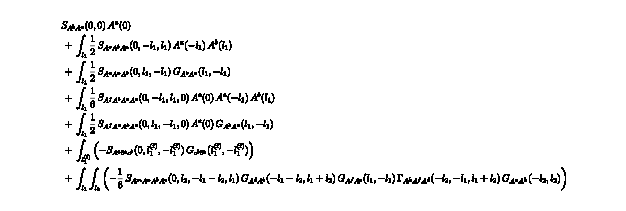

```mathematica
MakeDSE[A[x]]//FTruncate//FRoute//FPrint;
```

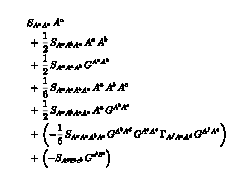

```mathematica
MakeDSE[A[x]]//FTruncate//FPrint;
```


-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

```mathematica
MakeDSE[A[x]]//FTruncate//FPlot;
```

## IV. Automatic Code Generation

```mathematica
parameterizations={
lf1->l1,cos[p,l1]->cospl1,

dressing[InverseProp,{A,A},1,{p1_,p2_}]:>ZA[Sqrt[sp[p2,p2]]]sp[p2,p2],
dressing[InverseProp,{A,A},2,{a_,b_}]:>xi^-1,
dressing[InverseProp,{cb,c},1,{p1_,p2_}]:>-Zc[Sqrt[sp[p2,p2]]]sp[p2,p2],

dressing[S,{A,A,A},1,{p1_,p2_,p3_}]:>gS,
dressing[S,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>gS^2,

dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[Sqrt[(sp[p1,p1]+sp[p2,p2]+sp[p3,p3])/3]],
dressing[GammaN,{A,cb,c},1,{p1_,p2_,p3_}]:>ZAcbc[Sqrt[(sp[p1,p1]+sp[p2,p2]+sp[p3,p3])/3]],

sp[l1,l1]:>l1^2,sp[p1,p1]:>p^2,sp[l1,p1]:>cospl1
};
parametrize[expr_]:=UseLorentzLinearity[expr//.parameterizations]//.parameterizations//Simplify;
```

```mathematica
MakeJuliaFunction[
Total@(DSEAAResult1L//parametrize)/.xi->0,
"Parameters"->{"l1","cos","p","Nc","gS","ZA","Zc","ZA3","ZAcbc","ZA4"},
"Name"->"DSE_kernel_AA_1Loop",
"Body"->"cospl1 = cos"
]
```

function DSE_kernel_AA_1Loop(l1, cos, p, Nc, gS, ZA, Zc, ZA3, ZAcbc, ZA4)
  cospl1 = cos
  _repl1 = ZA(sqrt(l1^2))
  _repl2 = l1^(-4)
  _repl3 = p^(-2)
  _repl4 = cospl1^2
  _repl5 = l1^2
  _repl6 = p^2
  _repl7 = l1^4
  _repl8 = p^4
  return (_repl2*_repl3*(-_repl4 + 7*_repl5*_repl6)*gS^2*Nc)/(3*_repl1) + (2*_repl2*_repl3*(_repl4*(7*_repl5*_repl6 + 3*_repl7 + 3*_repl8) - _repl5*_repl6*(8*_repl5*_repl6 + 3*_repl7 + 3*_repl8) - 6*_repl5*_repl6*(_repl5 + _repl6)*cospl1 + 6*(_repl5 + _repl6)*cospl1^3 + cospl1^4)*gS*Nc*ZA3(sqrt(0.6666666666666666)*sqrt(_repl5 + _repl6 + cospl1)))/(3*_repl1*(_repl5 + _repl6 + 2*cospl1)^2*ZA(sqrt(_repl5 + _repl6 + 2*cospl1))) + (_repl3*(_repl4 - _repl5*_repl6)*Nc*dressing(S,List(A,cb,c),1,List(p1,-l1 - p1,l1))*ZAcbc(sqrt(0.6666666666666666)*sqrt(_repl5 + _repl6 + cospl1)))/(3*(_repl5 + _repl6 + 2*cospl1)*l1^2*Zc(sqrt(_repl5))*Zc(sqrt(_repl5 + _repl6 + 2*cospl1)))
end

```mathematica
MakeCppFunction[
Total@(DSEAAResult1L//parametrize)/.xi->0,
"Parameters"->{"l1","cos","p","Nc","gS","ZA","Zc","ZA3","ZAcbc","ZA4"},
"Name"->"DSE_kernel_AA_1Loop",
"Body"->"const auto &cospl1 = cos;"
]
```

auto DSE_kernel_AA_1Loop(const auto &l1, const auto &cos, const auto &p, const auto &Nc, const auto &gS, const auto &ZA,
                         const auto &Zc, const auto &ZA3, const auto &ZAcbc, const auto &ZA4)
{
  const auto &cospl1 = cos;
  const auto _repl1 = ZA(sqrt(powr<2>(l1)));
  const auto _repl2 = powr<2>(l1);
  const auto _repl3 = powr<2>(p);
  const auto _repl4 = powr<-2>(p);
  const auto _repl5 = powr<2>(cospl1);
  const auto _repl6 = powr<4>(l1);
  const auto _repl7 = powr<4>(p);
  const auto _repl8 = powr<-4>(l1);
  return (0.3333333333333333) * ((7.) * ((_repl2) * (_repl3)) + (-1.) * (_repl5)) *
             ((powr<-1>(_repl1)) * ((_repl4) * ((_repl8) * ((powr<2>(gS)) * (Nc))))) +
         (0.6666666666666666) *
             (((7.) * ((_repl2) * (_repl3)) + (3.) * (_repl6) + (3.) * (_repl7)) * (_repl5) +
              (-1.) * ((8.) * ((_repl2) * (_repl3)) + (3.) * (_repl6) + (3.) * (_repl7)) * ((_repl2) * (_repl3)) +
              (-6.) * (_repl2 + _repl3) * ((_repl2) * ((_repl3) * (cospl1))) +
              (6.) * (_repl2 + _repl3) * (powr<3>(cospl1)) + powr<4>(cospl1)) *
             ((powr<-1>(_repl1)) *
              ((_repl4) *
               ((_repl8) * ((powr<-2>(_repl2 + _repl3 + (2.) * (cospl1))) *
                            ((gS) * ((Nc) * ((powr<-1>(ZA(sqrt(_repl2 + _repl3 + (2.) * (cospl1))))) *
                                             (ZA3((0.816496580927726) * (sqrt(_repl2 + _repl3 + cospl1))))))))))) +
         (0.3333333333333333) * ((-1.) * ((_repl2) * (_repl3)) + _repl5) *
             ((_repl4) *
              ((powr<-1>(_repl2 + _repl3 + (2.) * (cospl1))) *
               ((powr<-2>(l1)) * ((Nc) * ((dressing(S, List(A, cb, c), 1., List(p1, (-1.) * (l1) + (-1.) * (p1), l1))) *
                                          ((ZAcbc((0.816496580927726) * (sqrt(_repl2 + _repl3 + cospl1)))) *
                                           ((powr<-1>(Zc(sqrt(_repl2)))) *
                                            (powr<-1>(Zc(sqrt(_repl2 + _repl3 + (2.) * (cospl1))))))))))));
}